```mathematica
Clear[minx,miny,maxx,maxy]
minx = -π;
miny = -π;
maxx = π;
maxy = π;
```

```mathematica
Clear[sol,x,y,t, mu,tmin,tmax]
tmin = 0;
tmax = 10;
sigma = 0;
sol[x0_,y0_] := NDSolve[
{x'[t] == y[t],
y'[t]==-Sin[x[t]]- sigma y[t],
x[0]==x0,y[0]==y0},
{x,y},{t,tmin,tmax}]
```

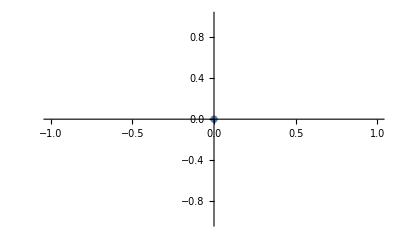

```mathematica
dist = 0.1;
initialCond = Join[
(*Table[{minx , y } , {y,miny , maxy,0.1}],
Table[{maxx, y} , {y, miny , maxy,0.1}],
Table[{x , miny},{x , minx , maxx,0.1}],
Table[{x,maxy},{x,minx , maxx,0.1}]*)

Table[{x , miny},{x , minx , maxx,dist}],
Table[{x,maxy},{x,minx , maxx,dist}],
Table[{minx , y } , {y,miny , maxy,dist}],
Table[{maxx, y} , {y, miny , maxy,dist}]
];
```

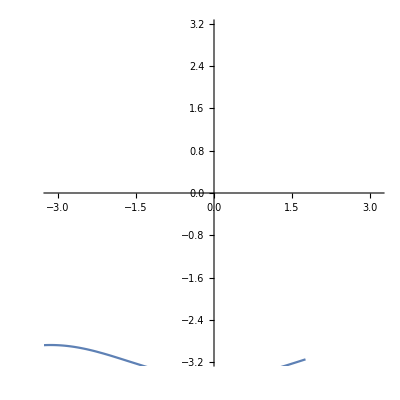

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/. sol[initialCond[[50,1]],initialCond[[50,2]]]],
{t,tmin,tmax}, PlotRange->{{minx,maxx},{miny,maxy}}]
```

```mathematica
p2 = Show[

Table[
ParametricPlot[
Evaluate[{x[t], y[t]}/.sol[initialCond[[i,1]], initialCond[[i,2
]]]],{t,tmin,tmax},PlotRange->{{minx,maxx},{miny,maxy}}],{i,1,Length[initialCond]}],
ListPlot[{{0,0}},PlotStyle->{PointSize[0.1],Red}, PlotMarkers->{"•",Large},PlotLegends->{"Center, σ=0"}]
]
```

-Graphics-

```mathematica
Show[p2,StreamPlot[{y,-Sin[x]-sigma*y},{x,-π,π},{y,-π,π}],PlotRange->{{minx,maxx},{miny,maxy}}]
```

-Graphics-

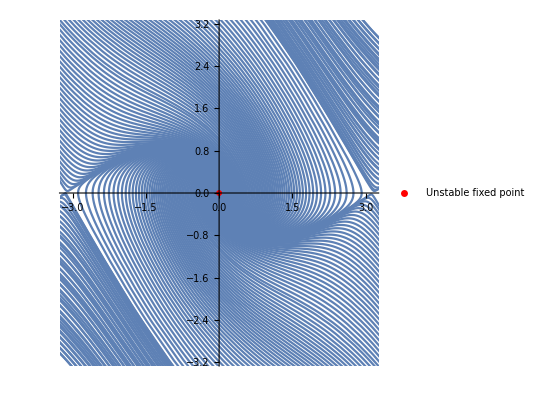
```mathematica
Show[-Graphics-,StreamPlot[{y,-Sin[x]-sigma *y},{x,-π,π},{y,-π,π}],PlotRange->{{-π,π},{-π,π}}]
```